```mathematica
ddc[x_,y_,z_,a_]:=(ⅇ^(((-Log[x])^a+(-Log[y])^a)^(1/a)-((-Log[x])^a+(-Log[y])^a+(-Log[z])^a)^(1/a)) (-1+a+((-Log[x])^a+(-Log[y])^a+(-Log[z])^a)^(1/a)) (((-Log[x])^a+(-Log[y])^a)/((-Log[x])^a+(-Log[y])^a+(-Log[z])^a))^(2-1/a))/(-1+a+((-Log[x])^a+(-Log[y])^a)^(1/a))
```

```mathematica
f2[x_,y_,z3_,a_]:=FindRoot[ddc[x,y,z,a]-z3,{z,0.0000000000001,1},Method->"Brent"][[1,2]]
```

```mathematica
Exit[]
```

```mathematica
A=20;Plot3D[f2[x,y,0.999,A],{x,of,1+of},{y,of,1+of},PlotPoints->30]
```

-Graphics3D-

```mathematica
A=20;nx=20;ny=20;of=0.000001;M=Flatten[Table[{{x/nx+of,y/ny+of},f2[x/nx+of,y/ny+of,0.999,A]},{x,0,nx},{y,0,ny}]//N,1];
M2=Flatten[Table[{x/nx+of,y/ny+of,f2[x/nx+of,y/ny+of,0.999,A]},{x,0,nx},{y,0,ny}]//N,1];
```

```mathematica
f3=Interpolation[M]
```

InterpolatingFunction[{{1.×10^-6,1.},{1.×10^-6,1.}},<>]

```mathematica
ListPointPlot3D[M2,PlotRange->All]
```

-Graphics3D-

```mathematica
h=Flatten[Table[x^n y^m,{n,0,3},{m,0,3}]]
```

{1,y,y^2,y^3,x,x y,x y^2,x y^3,x^2,x^2 y,x^2 y^2,x^2 y^3,x^3,x^3 y,x^3 y^2,x^3 y^3}

```mathematica
A[i_]:=D[D[#,{x,M[[i,1]]}],{y,M[[i,2]]}]&
```

```mathematica
Co=Inverse[Transpose[Flatten[Table[A[j][h]/.x->M[[i,1]]/.y->M[[i,2]],{j,4},{i,4}],1]]];Co//MatrixForm
```

(1 | 0 | -3 | 2 | 0 | 0 | 0 | 0 | -3 | 0 | 9 | -6 | 2 | 0 | -6 | 4
0 | 0 | 3 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | -9 | 6 | 0 | 0 | 6 | -4
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 9 | -6 | 0 | 0 | -6 | 4
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | -9 | 6 | -2 | 0 | 6 | -4
0 | 1 | -2 | 1 | 0 | 0 | 0 | 0 | 0 | -3 | 6 | -3 | 0 | 2 | -4 | 2
0 | 0 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | -3 | 0 | 0 | -2 | 2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -3 | 3 | 0 | 0 | 2 | -2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | -6 | 3 | 0 | -2 | 4 | -2
0 | 0 | 0 | 0 | 0 | 1 | -2 | 1 | 0 | -2 | 4 | -2 | 0 | 1 | -2 | 1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 1 | 0 | 0 | 2 | -2 | 0 | 0 | -1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | 0 | 0 | -1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 2 | -1 | 0 | 1 | -2 | 1
0 | 0 | 0 | 0 | 1 | 0 | -3 | 2 | -2 | 0 | 6 | -4 | 1 | 0 | -3 | 2
0 | 0 | 0 | 0 | 0 | 0 | 3 | -2 | 0 | 0 | -6 | 4 | 0 | 0 | 3 | -2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -3 | 2 | 0 | 0 | 3 | -2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 3 | -2 | 1 | 0 | -3 | 2)

```mathematica
Co[[1]]
```

{1,0,-3,2,0,0,0,0,-3,0,9,-6,2,0,-6,4}

```mathematica
h.Co[[1]]
```

1-3 x^2+2 x^3-3 y^2+9 x^2 y^2-6 x^3 y^2+2 y^3-6 x^2 y^3+4 x^3 y^3

```mathematica
s={0,3,1,-10,5,0,0,50,0,0,0,-10,-40};Plot3D[h.Sum[Co[[i]]*s[[i]],{i,Length[s]}],{x,0,1},{y,0,1}]
```

-Graphics3D-

```mathematica
Co=Table[KroneckerDelta[Ceiling[i/4] ,Ceiling[j/4]]*KroneckerDelta[Mod[i,4],Mod[j,4]],{i,16},{j,16}]//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

```mathematica
Ceiling[16/4]
```

4

```mathematica
Mod[7,4]
```

3

```mathematica
Table[c[i,j],{i,4},{j,4}]//MatrixForm
```

(c[1,1] | c[1,2] | c[1,3] | c[1,4]
c[2,1] | c[2,2] | c[2,3] | c[2,4]
c[3,1] | c[3,2] | c[3,3] | c[3,4]
c[4,1] | c[4,2] | c[4,3] | c[4,4])

```mathematica
Sum[Flatten[Table[x^n y^m,{n,0,3},{m,0,3}]][[i]]*c[j,i],{i,16}]
```

c[j,1]+y c[j,2]+y^2 c[j,3]+y^3 c[j,4]+x c[j,5]+x y c[j,6]+x y^2 c[j,7]+x y^3 c[j,8]+x^2 c[j,9]+x^2 y c[j,10]+x^2 y^2 c[j,11]+x^2 y^3 c[j,12]+x^3 c[j,13]+x^3 y c[j,14]+x^3 y^2 c[j,15]+x^3 y^3 c[j,16]

```mathematica
f[x_,y_,j_]:=c[j,1]+y c[j,2]+y^2 c[j,3]+y^3 c[j,4]+x c[j,5]+x y c[j,6]+x y^2 c[j,7]+x y^3 c[j,8]+x^2 c[j,9]+x^2 y c[j,10]+x^2 y^2 c[j,11]+x^2 y^3 c[j,12]+x^3 c[j,13]+x^3 y c[j,14]+x^3 y^2 c[j,15]+x^3 y^3 c[j,16]
```

```mathematica
M={{0,0},{0,1},{1,1},{1,0}};
```

```mathematica
A=.
```

```mathematica
A[4][x^2y]
```

2 x y

```mathematica
A[1][f[x,y,2]]/.x->M[[3,1]]/.y->M[[3,2]]
```

c[2,1]+c[2,2]+c[2,3]+c[2,4]+c[2,5]+c[2,6]+c[2,7]+c[2,8]+c[2,9]+c[2,10]+c[2,11]+c[2,12]+c[2,13]+c[2,14]+c[2,15]+c[2,16]

```mathematica
S1=Flatten[Table[(A[k][f[x,y,j*l]]/.x->M[[i,1]]/.y->M[[i,2]])==KroneckerDelta[i,j]*KroneckerDelta[k,l],{i,4},{j,4},{k,4},{l,4}],3];
```

```mathematica
S1//MatrixForm
```

```mathematica
Solve[S1,Flatten[Table[c[i,j],{i,16},{j,16}]]]
```

{}

```mathematica
Length[S2]
```

128

```mathematica
PiecewiseExpand[f3]
```

InterpolatingFunction[{{1.×10^-6,1.},{1.×10^-6,1.}},<>]

```mathematica
A=20;Plot3D[{f2[x,y,0.999,A],0.1+f3[x,y]},{x,0,1},{y,0,1},PlotPoints->20]
```

-Graphics3D-

```mathematica
g/.y->1/.x->1/.a->3
```

1.00023

```mathematica
ny
```

10

```mathematica
x=.
```

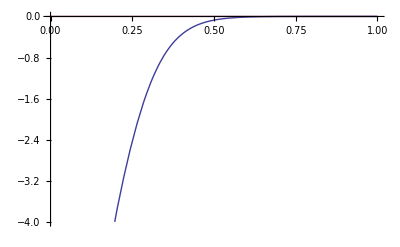

```mathematica
A=6;xx=0.3;yy=0.8;Plot[{Log[ddc[xx,yy,z,A]],0 g},{z,0,1},PlotRange->{-4,0}]
```

```mathematica
g=Normal[InverseSeries[Series[ddc[xx,yy,X,A],{X,0.4,55}]]//N]/.X->z];
```

```mathematica
g/.z->0.4
```

1.59248×10^15

```mathematica
g
```

0.4+0.187089 (0.355884+z)+0.236589 (0.355884+z)^2+0.43407 (0.355884+z)^3+0.898796 (0.355884+z)^4+1.99064 (0.355884+z)^5+4.60201 (0.355884+z)^6+10.9599 (0.355884+z)^7+26.677 (0.355884+z)^8+66.0277 (0.355884+z)^9+165.596 (0.355884+z)^10+419.78 (0.355884+z)^11+1073.59 (0.355884+z)^12+2766.23 (0.355884+z)^13+7172.9 (0.355884+z)^14+18701.7 (0.355884+z)^15+48993.6 (0.355884+z)^16+128891. (0.355884+z)^17+340346. (0.355884+z)^18+901700. (0.355884+z)^19+2.39607×10^6 (0.355884+z)^20+6.38421×10^6 (0.355884+z)^21+1.7052×10^7 (0.355884+z)^22+4.56472×10^7 (0.355884+z)^23+1.22444×10^8 (0.355884+z)^24+3.2906×10^8 (0.355884+z)^25+8.85858×10^8 (0.355884+z)^26+2.38862×10^9 (0.355884+z)^27+6.45022×10^9 (0.355884+z)^28+1.74422×10^10 (0.355884+z)^29+4.72266×10^10 (0.355884+z)^30+1.28025×10^11 (0.355884+z)^31+3.4745×10^11 (0.355884+z)^32+9.4395×10^11 (0.355884+z)^33+2.56707×10^12 (0.355884+z)^34+6.98771×10^12 (0.355884+z)^35+1.90378×10^13 (0.355884+z)^36+5.19112×10^13 (0.355884+z)^37+1.41661×10^14 (0.355884+z)^38+3.86871×10^14 (0.355884+z)^39+1.05728×10^15 (0.355884+z)^40+2.89143×10^15 (0.355884+z)^41+7.9125×10^15 (0.355884+z)^42+2.16662×10^16 (0.355884+z)^43+5.93618×10^16 (0.355884+z)^44+1.62733×10^17 (0.355884+z)^45+4.46351×10^17 (0.355884+z)^46+1.2249×10^18 (0.355884+z)^47+3.36311×10^18 (0.355884+z)^48+9.23815×10^18 (0.355884+z)^49+2.53879×10^19 (0.355884+z)^50+6.98002×10^19 (0.355884+z)^51+1.91986×10^20 (0.355884+z)^52+5.2827×10^20 (0.355884+z)^53+1.45416×10^21 (0.355884+z)^54+4.00433×10^21 (0.355884+z)^55

```mathematica
ddc[x,y,z,a]
```